```mathematica
(Λ={{γ,-γ*β,0, 0},
{-γ*β,γ,0,0},
{0,0,1,0},
{0,0,0,1}})//MatrixForm
```

(γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(F={{0,Ex,Ey,Ez},
{-Ex,0,Bz,- By},
{-Ey,-Bz,0,Bx},
{-Ez,By,-Bx,0}})//MatrixForm
```

(0 | Ex | Ey | Ez
-Ex | 0 | Bz | -By
-Ey | -Bz | 0 | Bx
-Ez | By | -Bx | 0)

```mathematica
Λ.F.Λ//Simplify//MatrixForm
%/.{(-1+β^2)->-1/γ^2}//FullSimplify//MatrixForm
```

(0 | -Ex (-1+β^2) γ^2 | (Ey-Bz β) γ | (Ez+By β) γ
Ex (-1+β^2) γ^2 | 0 | (Bz-Ey β) γ | -((By+Ez β) γ)
-Ey γ+Bz β γ | -Bz γ+Ey β γ | 0 | Bx
-((Ez+By β) γ) | (By+Ez β) γ | -Bx | 0)

(0 | Ex | (Ey-Bz β) γ | (Ez+By β) γ
-Ex | 0 | (Bz-Ey β) γ | -((By+Ez β) γ)
-Ey γ+Bz β γ | -Bz γ+Ey β γ | 0 | Bx
-((Ez+By β) γ) | (By+Ez β) γ | -Bx | 0)

```mathematica
(F1={{0,Ex,Ey,Ez},
{-Ex,0,Bz,- By},
{-Ey,-Bz,0,Bx},
{-Ez,By,-Bx,0}})//MatrixForm
```

(0 | Ex | Ey | Ez
-Ex | 0 | Bz | -By
-Ey | -Bz | 0 | Bx
-Ez | By | -Bx | 0)

```mathematica
(η={{-1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}})//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(F2=η.F1.η)//MatrixForm
```

(0 | -Ex | -Ey | -Ez
Ex | 0 | Bz | -By
Ey | -Bz | 0 | Bx
Ez | By | -Bx | 0)

```mathematica
F1.F2//MatrixForm
```

(Ex^2+Ey^2+Ez^2 | -Bz Ey+By Ez | Bz Ex-Bx Ez | -By Ex+Bx Ey
Bz Ey-By Ez | -By^2-Bz^2+Ex^2 | Bx By+Ex Ey | Bx Bz+Ex Ez
-Bz Ex+Bx Ez | Bx By+Ex Ey | -Bx^2-Bz^2+Ey^2 | By Bz+Ey Ez
By Ex-Bx Ey | Bx Bz+Ex Ez | By Bz+Ey Ez | -Bx^2-By^2+Ez^2)

```mathematica
Tr[F1.Transpose[F2]]//Simplify
```

2 (Bx^2+By^2+Bz^2-Ex^2-Ey^2-Ez^2)

```mathematica
-F1.η.F1.η//MatrixForm
```

(-Ex^2-Ey^2-Ez^2 | Bz Ey-By Ez | -Bz Ex+Bx Ez | By Ex-Bx Ey
-Bz Ey+By Ez | By^2+Bz^2-Ex^2 | -Bx By-Ex Ey | -Bx Bz-Ex Ez
Bz Ex-Bx Ez | -Bx By-Ex Ey | Bx^2+Bz^2-Ey^2 | -By Bz-Ey Ez
-By Ex+Bx Ey | -Bx Bz-Ex Ez | -By Bz-Ey Ez | Bx^2+By^2-Ez^2)

```mathematica
Tr[-F1.η.F1.η]
```

2 Bx^2+2 By^2+2 Bz^2-2 Ex^2-2 Ey^2-2 Ez^2

```mathematica
Integrate[1/(√(a^2-u^2)),u]
```

```mathematica
ArcTan[u/(√(a^2-u^2))]/.{u->0}
```

0

```mathematica
Integrate[c/(√(1-(1-c^2)Sin[ψ]^2)),ψ]
```

c EllipticF[ψ,1-c^2]

```mathematica
c EllipticF[0,1-c^2]
```

0

```mathematica
D[Tan[ϕ],ϕ]
```

Sec[ϕ]^2

```mathematica
Integrate[c/(√(1-c^2-x^2)(1-x^2)),x]
```

ArcTan[(c x)/(√(1-c^2-x^2))]

```mathematica
(c ArcTan[(√(1-a^2) x)/(√(a^2-x^2))])/(√(1-a^2))/.{x->0}
```

0

```mathematica
D[Tan[θ],θ]
```

Sec[θ]^2

```mathematica
Integrate[1/(√(1-c^2/r^2)),{r,c,R}]
```

ConditionalExpression[√(1-c^2/R^2) R, ]

```mathematica
Integrate[-1/(√(1-c^2/r^2)),r]
```

-√(1-c^2/r^2) r

```mathematica
(√(r^2-c^2))^2==( s+√(b^2-c^2) )^2//Expand
```

-c^2+r^2==b^2-c^2+2 √(b^2-c^2) s+s^2

```mathematica
Integrate[b/(s^2+b^2),{s,0,s}]
```

ConditionalExpression[ArcTan[s/b], Im[b/s]>1||Im[b/s]<-1||Re[b/s]≠0]

```mathematica
Integrate[(c*ⅇ^(x/a))/(√(c^2 ⅇ^(x/a)-1)),{x,x0,X}]
```

(2 a (√(-1+c^2 ⅇ^(X/a))-√(-1+c^2 ⅇ^(x0/a))))/c

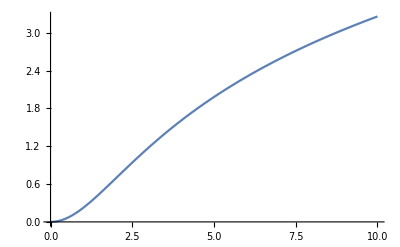

```mathematica
Plot[Log[1/4 t^2+1],{t,0,10}]
```

```mathematica
Integrate[1/(1/4(t/a)^2+1),{t,0,T}]
```

ConditionalExpression[2 a ArcCot[(2 a)/T], 2 Im[a/T]>1||Im[a/T]<-1/2||Re[a/T]≠0]

```mathematica
Limit[2 a ArcCot[(2 a)/T],T->∞]//PowerExpand
```

a π

```mathematica
Limit[2 a ArcCot[(2 a)/T],T->0]
```

0

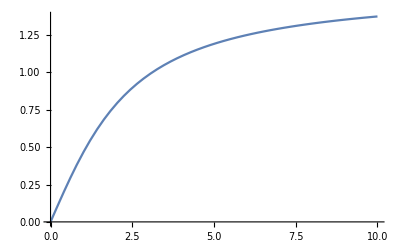

```mathematica
Plot[ArcCot[2/T],{T,0,10}]
```

```mathematica
Integrate[1/(√(ⅇ^(x/a)-1)),x]
```

2 a ArcTan[√(-1+ⅇ^(x/a))]

```mathematica
2 a ArcTan[√(-1+ⅇ^(x/a))]/.x->0
```

0

### P9.1

```mathematica
1.5*1.477
```

2.2155

```mathematica
2.2155*5/14.5^2
```

0.0526873

```mathematica
√((1-(2*2.2155)/17)/(1-(2*2.2155)/12))-1
```

0.0826729

### P9.2

```mathematica
1/(√(1-(2*1.02*1.477)/5640))-1
```

0.000267224

```mathematica
2.68*0.96
```

2.5728

```mathematica
2.68*1.06
```

2.8408

### P9.4

```mathematica
Integrate[(-2G*M)/(u^2 √(1-u)),u]
```

-2 G M (-(√(1-u))/u-ArcTanh[√(1-u)])

### P9.5

```mathematica
Integrate[1.0/(√(1-(2G*M)/r)),{r,3G*M,10G*M}]//Simplify
```

8.78253 G M

```mathematica
8.78/7
```

1.25429

### P9.7

```mathematica
D[R*Sinh[r/R],r]
```

Cosh[r/R]

```mathematica
D[R*ArcSinh[rr/R],rr]
```

1/(√(1+rr^2/R^2))

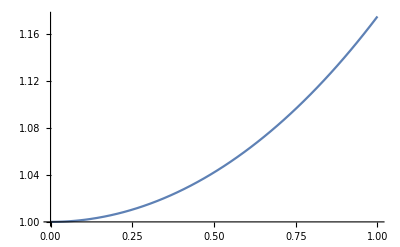

```mathematica
Plot[Sinh[x]/x,{x,0,1}]
```

```mathematica
Clear[v0];
Integrate[(v^2*ⅇ^(-v^2/v0^2))/(0.885837118847261 v0^3),{v,-3v0,3*v0}]
```

1.

```mathematica
Integrate[(v^2*ⅇ^(-v^2/v0^2))/(0.4429185594236306 v0^3),{v,0.0,V}]
```

```mathematica
ⅇ^-9.
```

0.00012341

```mathematica
Clear[v0];
Solve[D[(v^2*ⅇ^(-v^2/v0^2))/(0.4429185594236306 v0^3),v]==0,v]
(v^2*ⅇ^(-v^2/v0^2))/(0.4429185594236306 v0^3)/.v->v0
```

{{v→0.},{v→-1. v0},{v→1. v0}}

0.83058/v0

8.3058

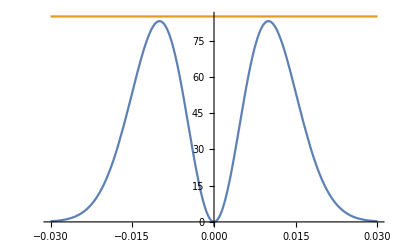

```mathematica
v0=0.01;
Plot[{(v^2*ⅇ^(-v^2/v0^2))/(0.4429185594236306 v0^3),0.85/v0},{v,-3v0,3v0}]
```

```mathematica
kg=eV
```

```mathematica
10^9/(5.61*10^35)
```

1.78253×10^-27

```mathematica
√(3/(8*π*7.426*10^-28 m/kg*ρ*Gev^4))H/Mpc
```

```mathematica
(1.267836425454463*^13 H √(kg/(1.78*10^-36*10^9 kg*Gev^3 m ρ)))/Mpc
```

```mathematica
(3.005060527451471*^26 H √(1/(Gev^2 10^9* 5.07*10^6 ρ)))/Mpc//PowerExpand
```

```mathematica
(4.220357532188572*^18 H)/(10^9*10^6*1.56*10^23 √ρ)
```

(2.70536×10^-20 H)/(√ρ)

```mathematica
45.7*10^9*365*24*3600*3*10^8*3.24*10^-17/10^6
```

14008.4

```mathematica
ψ[x_]:=3/x^2(Sin[x]/x-Cos[x])
```

```mathematica
Limit[ψ[x],x->0]
```

1

```mathematica
Series[ψ[x],{x,0,3}]
```

1-x^2/10+O[x]^4

```mathematica
Limit[ψ'[x],x->0]
```

0

```mathematica
Series[ψ'[x],{x,0,3}]
```

-x/5+x^3/70+O[x]^4

```mathematica
Gev=10^3 Mev;
fp0*Hz==10^-9 Hz*(Ts*Gev)/(10.0Mev)
Solve[%,fp0]
```

fp0 Hz==1.×10^-7 Hz Ts

{{fp0→1.×10^-7 Ts}}

```mathematica
Gev=10^3 Mev;
c((σ^(1/3)Gev)/(10^5 Gev))^3((10.0Mev)/(Ts*Gev))^2
```

(1.×10^-19 c σ)/Ts^2